This notebook combines niche and food-web models

predators have a trophic link to all herbivores, the foraging efficiency is currently the bodymass probability of interaction

```mathematica
(* The allometrically determined niche model*)
(* Interactions function takes lists of organisms and masses, returns an interaction matrix*)
interactions[numPlants_,herbList_,predList_,connectance_,model_]:=Module[
{},

(* sets number of consumers and number of species based on trophic levels *)
numHerb=Length[herbList];
numPred=Length[predList];
numSpp=numPlants+numHerb+numPred;

(* beta paramter for generating niche model ranges is derived from connectance*)
beta=((1/(2*connectance)) - 1);
alpha=1;

(* herbivore masses are drawn as random exponent in the order of magnitude range we are interested in 1kg->10,000kg*)
(*herbMassExp = Sort[RandomVariate[UniformDistribution[{0,4}], numHerb]];
herbMassList=Map[massFunc,herbMassExp];*)

herbMassList=Sort[herbList];

(* predator masses drawn between 1kg and 500kg*)
     (*predMassList =Sort[RandomVariate[UniformDistribution[{1.0,500.0}], numPred]]*);

predMassList=Sort[predList];

(* combined list of bodymasses for predators and herbivores *)
bodyMassList=Join[herbMassList,predMassList];

(* find the largest organism to set the log scale*)
maxMass=Max[bodyMassList];
maxLogMass=Log10[Max[bodyMassList]];
minLogMass=Log10[Min[bodyMassList]];

(* randomly draw plant niches from uniform 0-1 *)
plantNicheValue=Sort[RandomVariate[UniformDistribution[{0,1.0}], numPlants]];

(* convert the log of herbiore mass to a niche value (i think this undoes the original conversion from an exponent to a mass)*)
herbNicheValue=Sort[Table[
logMassToNiche[herbMassList[[i]]],
{i,1,numHerb}]];

(* convert the log of predator mass to a niche value*)
predNicheValue=Sort[Table[
logMassToNiche[predMassList[[i]]],
{i,1,numPred}]];

(* each species is given a unique Int ID number which is interlaced with it's niche value*)
plantID=Table[i,{i,1,numPlants}];
herbID=Table[i,{i,numPlants+1,numSpp-numPred}];
predID=Table[i,{i,numPlants+numHerb+1,numSpp}];

(* these niche variables combine a unique ID integer with niche or bodymass*)
plantNiche=Thread[{plantID,plantNicheValue}];
herbNiche=Thread[{herbID,herbNicheValue,herbMassList}];
predNiche=Thread[{predID,predNicheValue, predMassList}];





(* Sets the width (level of generalism) of consumers based on their niche value and a Beta draw*)
herbNicheRange=Table[ 
If[model==1,
parabolicNicheModelRange[{herbNiche[[i,2]]}],  
inverseNicheModelRange[{herbNiche[[i,2]]}]],
{i, 1, numHerb}];

(* Finds the center of the trophic niche for herbivores *)
herbNicheCenter = Table[
RandomReal[Flatten[{herbNicheRange[[i]]/2,herbNiche[[i,2]]}]],
{i,1,numHerb}];

(* combines the center of the trophic niche with the range to create specific min/max values for plant prey *)
herbNicheMin =Flatten[Table[herbNicheCenter[[i]]-herbNicheRange[[i]]/2,{i,1,numHerb}]];
herbNicheMax =Flatten[Table[herbNicheCenter[[i]]+herbNicheRange[[i]]/2,{i,1,numHerb}]];





(* adds trophic link between predator and herbivore stochastically via bodysize model *)
predPreyLink=Table[
x=predNiche[[i,3]];
y=herbNiche[[j,3]];
(*If[RandomReal[]<probInteract[x,y],
herbNiche[[j,1]],
Nothing],*)
herbNiche[[j,1]],
{i,1,numPred},{j,1,numHerb}];

(* *)
predLink=Table[
Join[predPreyLink[[i]]],
{i,1,numPred}];

(* adds trophic links between herbivores and plants deterministcally if plant niche falls within herb niche range*)
herbPlantLink=Table[
If[plantNiche[[j,2]]>herbNicheMin[[i]]&&plantNiche[[j,2]]<herbNicheMax[[i]],
plantNiche[[j,1]],
Nothing],
{i,1,numHerb},{j,1,numPlants}];

plants=Table[{}, {i,1,numPlants}];

(* totals number of prey links each predator has*)
predNumberPrey=Table[
{predNiche[[i,2]],
Length[Flatten[predLink[[i]]]]},
{i,1,numPred}];

(* totals number of plant links each herbiovre has*)
herbNumberPlants=Table[
{herbNiche[[i,3]],
Length[Flatten[herbPlantLink[[i]]]]},
{i,1,numHerb}];

(* gets plant data in proper form for joining with pred and herb data*)
plants =Table[
{plantNiche[[i,1]],
{}},
{i,1,numPlants}];

(* joins predator generality to niche values*)
predators =Table[
{predNiche[[i,1]],
predLink[[i]]},
{i,1,numPred}];

(* joins herbivore generality to niche values*)
herbivores=Table[
{herbNiche[[i,1]],
herbPlantLink[[i]]},
{i,1,numHerb}];

(* joins organism data together*)
preyList = Join[plants,herbivores,predators];


(* assembles interaction data into an interaction matrix *)
foodWeb = Table[
If[MemberQ[preyList[[i,2]],j],
1,
0],
{i,1,numSpp},
{j,1,numSpp}
];

Join[(*predNumberPrey,*)herbNumberPlants]

] (* this is the end of the interactions function *)


(* some helper functions *)
(*logMassToNiche[x_]:=Log10[x]/maxLogMass;*)
logMassToNiche[x_]:=(Log10[x]-minLogMass)/(maxLogMass-minLogMass);
massFunc[x_]:=10^x; (* used to draw body masses after randomly generating exponents*)

(* functions for determining the range of a consumer niche*)
randRange[]:=RandomReal[]*RandomVariate[BetaDistribution[alpha,beta]]
nicheModelRange[x_]:=x*RandomVariate[BetaDistribution[alpha,beta]]
inverseNicheModelRange[x_]:=(1-x)*RandomVariate[BetaDistribution[alpha,beta]]
parabolicNicheModelRange[x_]:=(4*(x-0.5)^2+0.2)*RandomVariate[BetaDistribution[alpha,beta]]

(* probability of interaction functions for predator/prey interactions *)
(* body size model parameterized by egypt paper *)
(* x is pred mass, y is prey mass *)
bodySizeModel[x_,y_]:=Exp[1.41+3.73*Log[x/y]+(-1.87)*Log[x/y]^2]
probInteract[x_,y_]:=bodySizeModel[x,y]/(1+bodySizeModel[x,y])
```

```mathematica
(* Lambert 1998 data for modern mammals in california*)
herbsModern={0.008,0.013,0.027,0.029,0.044,0.051,0.070,0.092,0.160,0.250,0.509,0.652,0.695,0.914,2.485,93.000,0.857,0.985,2.586};
predsModern={0.005,0.005,0.023,0.075,0.176,4.600,5.060,11.000,18.000,80.000,5.300,180.000};
(* interactions function returns an interaction matrix or table of mass and generality *)
interactions[25,herbsModern,predsModern,0.171,1]
```

{{0.008,0},{0.013,6},{0.027,11},{0.029,3},{0.044,3},{0.051,1},{0.07,11},{0.092,0},{0.16,2},{0.25,4},{0.509,0},{0.652,0},{0.695,1},{0.857,0},{0.914,2},{0.985,1},{2.485,0},{2.586,0},{93.,13}}

```mathematica
(* Lambert 1998 data for pleistocene mammals in california*)
herbsPleist={40.0,1015.0,1035.0,995.0,21.0,316.0,0.051,221.0,616.0,1990.0,196.0,2.485,5761.0,9407.0,1320.0,0.70,0.250,614.0,93.0,0.27,0.22,75.0,0.013,0.914,0.509,0.695,0.160,0.985,2.586,0.857};
predsPleist={372.0,51.500,11.000,80.000,271.000,18.000,0.176,0.005,0.023,298.000,0.075,164.000,0.005,5.060,4.600,5.300,180.000,455.000}
interactions[25,herbsPleist,predsPleist,0.171,1]
```

{372.,51.5,11.,80.,271.,18.,0.176,0.005,0.023,298.,0.075,164.,0.005,5.06,4.6,5.3,180.,455.}

{{0.013,5},{0.051,5},{0.16,1},{0.22,4},{0.25,1},{0.27,5},{0.509,0},{0.695,2},{0.7,1},{0.857,1},{0.914,0},{0.985,1},{2.485,0},{2.586,0},{21.,1},{40.,3},{75.,3},{93.,11},{196.,5},{221.,0},{316.,5},{614.,0},{616.,8},{995.,3},{1015.,15},{1035.,4},{1320.,4},{1990.,14},{5761.,10},{9407.,7}}

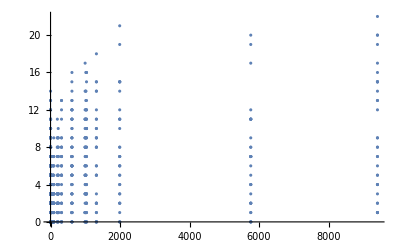

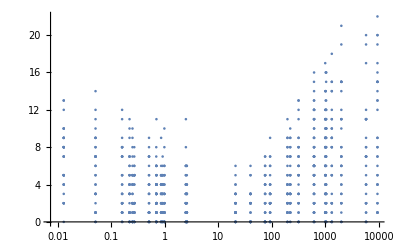

```mathematica
(* function for running simulations of the interaction function 
   output is bodymass and generality of herbivore species *)
sim[numPlants_,herbList_,predList_,connectance_,model_,num_]:=Table[interactions[numPlants,herbList,predList,connectance,model],{num}];

numberPrey=sim[25,herbsPleist,predsPleist,0.171,1,1000]; (* runs the sim function to collect generality data *)

(* makes figues of mass-generality association*)
p1=Table[{Flatten[numberPrey,1][[i,1]],Flatten[numberPrey,1][[i,2]]},{i,1,1000}];
(*AxesLabel->{Mass,# of prey},PlotLabel->"Herbivore Generality by Mass:  Niche Model",*)
ListPlot[p1//N,PlotRange->All]
ListLogLinearPlot[p1//N,PlotRange->All]
```

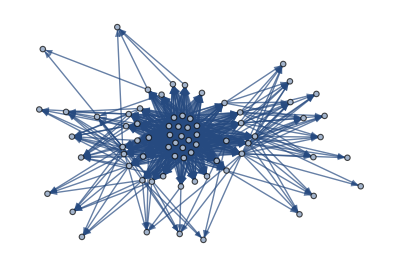

SparseArray[…]

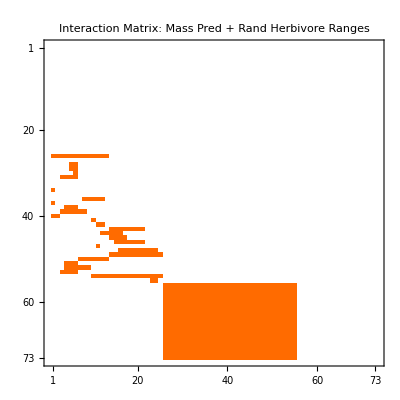

```mathematica
interactions[25,herbsPleist,predsPleist,0.171,1];
adjG =AdjacencyGraph[foodWeb]
adjM = AdjacencyMatrix[adjG]
MatrixPlot[adjM,PlotLabel->"Interaction Matrix: Mass Pred + Rand Herbivore Ranges"]
foodWeb;
```

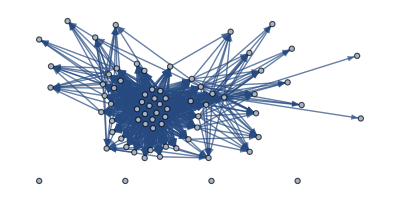

-Graphics-

```mathematica
(* generateFW takes the interaction matrix produced by "interactions" and generates a dynamical system *)
generateFW[ numPlants_,herbList_,predList_,adjM_,perAdaptive_]:= Module[
{},
numHerb=Length[herbList];
numPred=Length[predList];
numSpp=numPlants+numHerb+numPred;
(*Define percent adaptive foragers*)
PerAdaptive = perAdaptive;     (**)
G = Table[       (* build vector of learning rates *)
rr=RandomReal[];
If[rr<PerAdaptive,      (*if random number is less than % adaptive species*)
(*RandomVariate[UniformDistribution[{0.0,5}]],*)   (*draw from a 0-5 random uniform*)
0.25, (* defaulting to 0.25*)
0                                                           (*otherwise set value to 0*)
],{i,1,numSpp}];    (* run the if-statement for each i in 1:numberspecies*)

(*Randomly assign foraging efficiencies*)
(* from Pires 2015- q=a*y*e^-(mi-mj)^2, y is rand normal u=1 s=1 *)
(* currently produces negative values*)
(*f = Table[
If[i ≠ j,    (* if predator and prey sepcies aren't the same*)
RandomVariate[UniformDistribution[{0,1}]],(**Exp[-(SppMass[[i]]-SppMass[[j]]^2)],*) (* draw a random foraging efficiency value 0-1*)
0    (* set to 0 if it is the same species*)
],{i,1,numSpp},{j,1,numSpp}];*) (* get a value for every possible species interaction*)


f=Table[
(* takes the probability of interaction as uses it as a foraging efficiency*)
If[i>numPlants+numHerb && j>numPlants && j≤ numPlants+numHerb,  (* if i is a predator*)
(* x and y here are massess and not niche values, position 3 in predNiche and herbNiche are mass values*)
x=predNiche[[i-(numPlants+numHerb),3]];
y=herbNiche[[j-numPlants,3]];
probInteract[x,y],

If[i>numPlants && i≤ numPlants+numHerb && j ≤ numPlants,(* if i is a herbivore *)
RandomVariate[UniformDistribution[{0,1}]],(* f for herbs is rand*)
0 
]
],
{i,1,numSpp},{j,1,numSpp}
];


(*r = Table[       (* build vector of learning rates *)
   RandomReal[{0.1,2.0}],{i,1,numSpp}];    *)
r = Table[       (* build vector of learning rates *)
If[i≤ numPlants,
RandomReal[{0.1,2.0}]
(*RandomReal[{2.81*^-10,2.19*^-8}]*), (* justin's value 1/s from starvation paper*)
   0],{i,1,numSpp}
]; 

(* assimilation efficiency from yodzis and Innes 1992*)
e = Table[       (* build vector of assimilation efficiencies *)
If[i ≤ numPlants,
0.0,
If[i ≤ numPlants+numHerb,
0.45,
   0.85]],{i,1,numSpp}
];

(
(*Declare parameter values*)
(*r=0.8;*)  (* intrinsic growth *)
s=1;     (* self limitation/intraspecific competition*)
(*e=0.15; (* conversation efficiency*)*)
T = 100000;  (* this is t max 10^5 *)

(*Define population equations*)
eqnX =       (* create a table of equations *)
Table[{
Subscript[X, i]'[t] ==   (* each equation is for x-sub-i, ODE wrt t *)
Subscript[X,i][t]*      (* current pop density multiplied by...*)
(r[[i]]-s*Subscript[X,i][t] + (* intrinsic growth minus self limitation*)
(* sum of gains from consuming prey: 0/1 interation x foraging effort x prey density*)
Sum[adjM[[i,j]]*e[[i]]*f[[i,j]]*Subscript[a, i,j][t]* Subscript[X, j][t], {j,1,numSpp }]- 
(* sum of losses to predation: 0/1 interation x foraging effort x pred density*)
Sum[adjM[[j,i]]*f[[j,i]]*Subscript[a, j,i][t]* Subscript[X, j][t], {j,1,numSpp }])},{i,1,numSpp}];

(*Define foraging effort equations*)
eqnA =   (* build matrix of foraging effort equations*)
Table[{
Subscript[a, i,j]'[t] ==
adjM[[i,j]]* (* if there isn't an interaction, the equation will = 0*)(G[[i]]*Subscript[a, i,j][t] * (* learning rate x current effort*)
(* conversion x foraging efficiency x prey density with assumption of 100% foraging effort *)
(e[[i]]*f[[i,j]]*Subscript[X,j][t] -
(* sum of current foraging effort x conversion x efficiency x prey density for all prey interactions*)
 Sum[adjM[[i,k]]*Subscript[a, i,k][t]*e[[i]]*f[[i,k]]*Subscript[X,k][t], {k,1,numSpp }]))},{i,1,numSpp},{j,1,numSpp}];

(*Declare starting conditions*)
startcond =  (* joins and flattens a table of init pop densities (0-0.1) with a table of normalized init foraging efforts*)Flatten[Join[{Table[Subscript[X, i][0]==RandomVariate[UniformDistribution[{0,0.1}]], {i,1, numSpp}],Table[Subscript[a, i,j][0]==
If[Total[adjM[[i,All]]]>0,
adjM[[i,j]]*RandomVariate[UniformDistribution[{0,1}]]/Total[adjM[[i,All]]],
0], 
{i,1, numSpp},{j,1, numSpp}]}]];

(*Mathematica weirdness*)
varsX = Table[Subscript[X, i][t], {i,1, numSpp}];(* makes vector of species variables*)
varsA= Table[Subscript[a, i,j][t], {i,1, numSpp}, {j,1, numSpp}]; (* makes vector of foraging effort variables*)
vars = Flatten[Join[varsX,{varsA}]]; (* makes one flat vector of variables out of species and efforts*)
eqns =Flatten[Join[eqnX,eqnA,startcond]]; (* makes one flat list of equations and initial conditions*)

(*This step solves the equations*)
sol=NDSolve[eqns, vars, {t,1,T}](* solves equations from 1 to time T *)
)(*//Timing*)
]
```

```mathematica
(* combines interactions and generateFW into a single function call, outputs a dynamical system *)
fullModel[numPlants_,herbList_,predList_,connectance_,model_,perAdaptive_]:=Module[
{},
interactions[numPlants,herbList,predList,connectance,model];
adjG =AdjacencyGraph[foodWeb];
adjM = AdjacencyMatrix[adjG];
MatrixPlot[adjM,PlotLabel->"Interaction Matrix: Mass Pred + Rand Herbivore Ranges"];

generateFW[ numPlants,herbList,predList,adjM,perAdaptive]
(*LogLinearPlot[Evaluate[varsX/.sol],{t,1,T},AxesOrigin->{0,0},AspectRatio->0.5,PlotRange->All,Frame->True]*)

]
```

```mathematica
output=fullModel[10,herbsPleist,predsPleist,0.3,1,0.5]; (* generate sample DS with modern california data*)
```

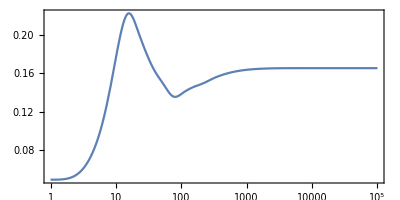

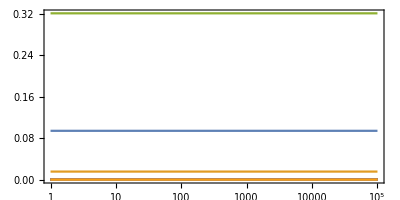

```mathematica
(*Plot foraging effort for species i*)
(* 1-129 plants, 130-153 herbs, 154-159 preds*)
i=26;
LogLinearPlot[Evaluate[varsX[[i,All]]/.sol],{t,1,T},AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->All,Frame->True]
LogLinearPlot[Evaluate[varsA[[i,All]]/.sol],{t,1,T},AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->All,Frame->True]
```

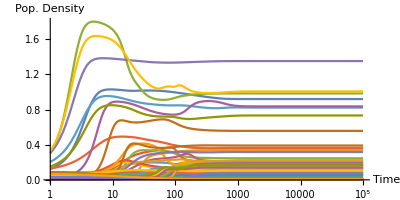

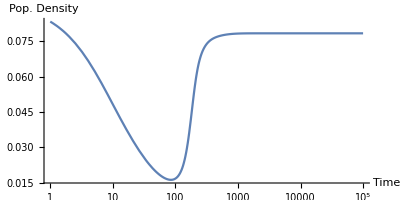

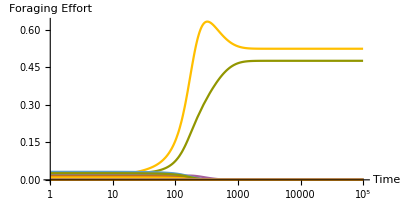

```mathematica
(*Plot Populations over time*)
LogLinearPlot[Evaluate[varsX/.sol],{t,1,T},AxesOrigin->{0,0},AspectRatio->0.5,PlotRange->All,AxesLabel->{"Time","Pop. Density"}]
(*Plot foraging effort for species i*)
(* 1-129 plants, 130-153 herbs, 154-159 preds*)
i=50;
LogLinearPlot[Evaluate[varsX[[i,All]]/.sol],{t,1,T},AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"Time","Pop. Density"}]
LogLinearPlot[Evaluate[varsA[[i,All]]/.sol],{t,1,T},AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"Time","Foraging Effort"}]
```

```mathematica
finalPops=Table[output[[1,i]][[2]]/.t->50000, {i,1,numSpp}]


finalForage=Table[output[[1,i]]/.t->50000, {i,numSpp+1,Dimensions[output][[2]]}]
```

{0.919875,0.12362,0.983761,0.363603,1.3523,0.55748,0.822754,1.00691,0.83638,0.732943,0.212892,0.151188,0.201302,0.0520888,0.031764,0.058103,0.338078,0.245208,0.0852499,0.124692,-1.45827×10^-12,0.189352,0.113501,0.0704542,0.133987,0.16521,0.0530939,0.170842,0.218652,0.071357,0.0529045,0.21878,0.0105756,0.0870172,0.316353,0.390813,0.134647,0.0978728,0.18915,0.0184212,0.00372874,0.000098444,0.17178,0.00485052,0.00730049,0.01764,0.0128115,0.162721,0.00176939,0.0783507,0.00376266,0.00616299,0.137813,0.138697,0.170708,0.0108821,0.00999331,0.00821387}

{a_(1,1)[50000]→0.,a_(1,2)[50000]→0.,a_(1,3)[50000]→0.,a_(1,4)[50000]→0.,a_(1,5)[50000]→0.,a_(1,6)[50000]→0.,a_(1,7)[50000]→0.,a_(1,8)[50000]→0.,a_(1,9)[50000]→0.,a_(1,10)[50000]→0.,a_(1,11)[50000]→0.,a_(1,12)[50000]→0.,a_(1,13)[50000]→0.,a_(1,14)[50000]→0.,3337,a_(58,46)[50000]→0.,a_(58,47)[50000]→0.,a_(58,48)[50000]→0.,a_(58,49)[50000]→0.,a_(58,50)[50000]→0.,a_(58,51)[50000]→0.,a_(58,52)[50000]→0.,a_(58,53)[50000]→0.,a_(58,54)[50000]→0.,a_(58,55)[50000]→0.,a_(58,56)[50000]→0.,a_(58,57)[50000]→0.,a_(58,58)[50000]→0.}
 |  |  |  |

```mathematica
(* find what proportion of species survive to t=50k *)
Count[finalPops, x_/;x>0.001]

surviving=N[Count[finalPops, x_/;x>0.001]/numSpp]
```

56

0.965517

```mathematica
(* function for generating many foodwebs and assessing final proportion surviving species*)
multiRunStability[numPlants_,herbList_,predList_,connectance_,model_,perAdaptive_,num_]:=Module[
{},
output=ParallelTable[fullModel[numPlants,herbList,predList,connectance,model,perAdaptive],{num}];
finalPops=ParallelTable[output[[j,1,i]][[2]]/.t->50000,{j,1,num}, {i,1,numSpp}];
Table[N[Count[finalPops[[i]], x_/;x>0.001]/numSpp],{i,1,num}]
]

stability=multiRunStability[10,herbsModern,predsModern,0.3,1,0.5,1];
```

```mathematica
(* 25 run mean survival proportions
pliestocene - 0.8503448275862069
modern      - 0.6186206896551726

 *)

survival=Mean[stability]
```

0.603448

```mathematica
Dimensions[stability]
stability
```

{1}

{0.603448}

```mathematica
(* ****** NEW STUFF ****** *)
(* To do:
- average the interpolating functions
- compare holocene vs pliestocene 
- figure out a good figure for results
*)
```

```mathematica
(* multiRun function generates num runs of the interaction matrix and resulti *)
multiRun[numPlants_,herbList_,predList_,connectance_,model_,perAdaptive_,num_]:=ParallelTable[fullModel[numPlants,herbList,predList,connectance,model,perAdaptive];
(*Table[output[[1,i]][[2]]/.t->50000, {i,1,numSpp}]*)
,{num}];
```

```mathematica
wat=multiRun[10,herbsPleist,predsPleist,0.3,1,0.5,10];  (* generates 10 dynamical systems, each as ~1700 interpolating functions*)
```

```mathematica
Dimensions[wat] (* check that dimensions are what is expected*)
```

{10}

```mathematica
(* this appears to successfully combine two interpolating fucntions. graphed results don't make sense though*)
(*f=FunctionInterpolation[output[[1,1]][[2]],{t,1,T}];
g=FunctionInterpolation[output[[1,2]][[2]],{t,1,T}];
h=FunctionInterpolation[{output[[1,1]][[2]]+output[[1,2]][[2]]},{t,1,T}]*)
```

```mathematica
LogLinearPlot[Evaluate[{f[t],g[t],{f[t]+g[t]}/2,h[t]}],{t,1,T},AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->All,Frame->True]
```

-Graphics-

```mathematica
h=ListInterpolation[Table[{f[t]+g[t]},{t,1,T}]]
```

InterpolatingFunction[{{1, 100000}}, <>]

```mathematica
(*(* makes a table of just the interpolating functions for population densities *)
blep=ParallelTable[FunctionInterpolation[wat[[i,1,j]][[2]],{t,1,T}],{i,1,10},{j,1,numSpp}];*)
```

```mathematica
Dimensions[blep]
```

{}

```mathematica
blep;
```

```mathematica
(* make a table of values at which to evaluate the population densities*)
ones=Table[i, {i,1,100}];
twos=Table[100+2*i,{i,1,200}];
fives=Table[500+5*i,{i,1,200}];
tens=Table[1500+10*i,{i,1,350}];
hundreds=Table[5000+100*i,{i,1,450}];
values=Join[ones,twos,fives,tens,hundreds];
```

```mathematica
(*(* makes a table of the population densities at time steps*)
blop=ParallelTable[
{t,
Sum[blep[[i,j]][t],{i,1,10}]/10},
{j,1,numSpp},
{t,values}
];*)
```

```mathematica
Dimensions[blop]
```

{}

```mathematica
(*Export["pleistocene_cal_run.csv",blop,"MAT"];*)
```

```mathematica
blap=Import["pleistocene_cal_run.csv","MAT"];
Dimensions[blap]
 blap;
```

{58,1300,2}

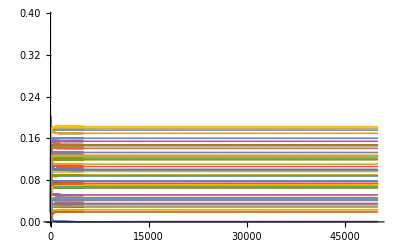

```mathematica
ListPlot[blap]
```

```mathematica
10
Length[herbsPleist]
Length[predsPleist]
```

10

30

18

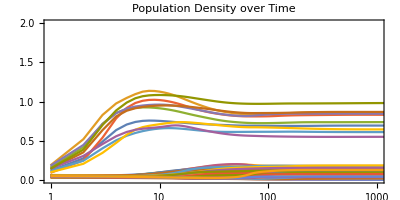

```mathematica
colorList={green,blue,red};
ListLogLinearPlot[blap,AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->{{1,1000},{0,2.0}},Frame->True, Joined->True,
PlotLabel->"Population Density over Time"(*,PlotStyle->colorList*)]
```

```mathematica
green=Table[Green,{10}];
blue=Table[Blue,{30}];
red=Table[Red,{18}];
```

```mathematica
plants=Table[blap[[i]],{i,1,10}];
herbs=Table[blap[[i]],{i,11,40}];
preds=Table[blap[[i]],{i,41,58}];
```

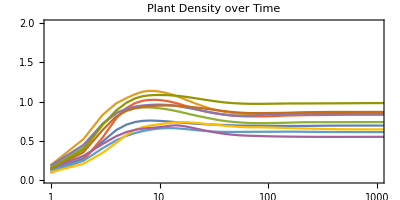

```mathematica
ListLogLinearPlot[plants,AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->{{1,1000},{0,2.0}},Frame->True, Joined->True,PlotLabel->"Plant Density over Time"]
```

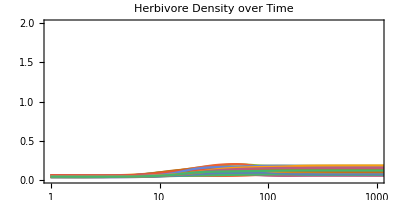

```mathematica
ListLogLinearPlot[herbs,AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->{{1,1000},{0,2.0}},Frame->True, Joined->True,PlotLabel->"Herbivore Density over Time"]
```

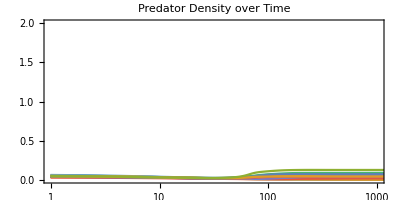

```mathematica
ListLogLinearPlot[preds,AspectRatio->0.5,AxesOrigin->{0,0},PlotRange->{{1,1000},{0,2.0}},Frame->True, Joined->True,PlotLabel->"Predator Density over Time"]
```

```mathematica
Length[plants]
```

10

```mathematica
Last[plants[[1]]][[2]]
```

0.692941

```mathematica
herbDensities=Table[Last[herbs[[i]]][[2]],{i,1,30}]
```

{0.106089,0.160189,0.179482,0.0778282,0.145961,0.0989135,0.0679848,0.12634,0.0719917,0.0984261,0.0687519,0.0876846,0.096462,0.0517554,0.0648847,0.0713422,0.0987076,0.110527,0.126405,0.122395,0.100675,0.169724,0.12754,0.140903,0.133028,0.14797,0.175843,0.182703,0.154393,0.119215}

```mathematica
predDensities=Table[Last[preds[[i]]][[2]],{i,1,18}]
```

{0.000719913,0.000322669,0.0232517,0.0290033,0.066316,0.0780176,0.0409697,0.0299246,0.0464029,0.034392,0.0189822,0.044433,0.0711462,0.0352984,0.0894409,0.0739049,0.0419982,0.12638}

```mathematica
herbTable=Table[{herbsPleist[[i]],herbDensities[[i]]},{i,1,30}]
```

{{40.,0.106089},{1015.,0.160189},{1035.,0.179482},{995.,0.0778282},{21.,0.145961},{316.,0.0989135},{0.051,0.0679848},{221.,0.12634},{616.,0.0719917},{1990.,0.0984261},{196.,0.0687519},{2.485,0.0876846},{5761.,0.096462},{9407.,0.0517554},{1320.,0.0648847},{0.7,0.0713422},{0.25,0.0987076},{614.,0.110527},{93.,0.126405},{0.27,0.122395},{0.22,0.100675},{75.,0.169724},{0.013,0.12754},{0.914,0.140903},{0.509,0.133028},{0.695,0.14797},{0.16,0.175843},{0.985,0.182703},{2.586,0.154393},{0.857,0.119215}}

```mathematica
predTable=Sort[Table[{predsPleist[[i]],predDensities[[i]]},{i,1,18}]]
```

{{0.005,0.0299246},{0.005,0.0711462},{0.023,0.0464029},{0.075,0.0189822},{0.176,0.0409697},{4.6,0.0894409},{5.06,0.0352984},{5.3,0.0739049},{11.,0.0232517},{18.,0.0780176},{51.5,0.000322669},{80.,0.0290033},{164.,0.044433},{180.,0.0419982},{271.,0.066316},{298.,0.034392},{372.,0.000719913},{455.,0.12638}}

0.121665-6.98959×10^-6 t

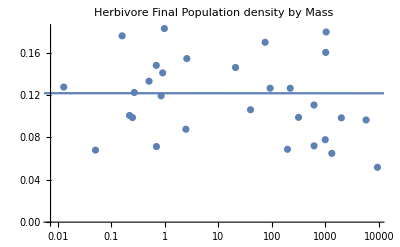

```mathematica
line=Fit[Sort[herbTable],{1,t},t]
Show[ListLogLinearPlot[Sort[herbTable],Joined->False,PlotLabel->"Herbivore Final Population density by Mass"],Plot[line,{t,-10,1000}]]
```

0.0429125+0.0000409653 t

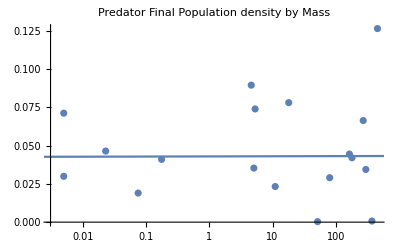

```mathematica
line=Fit[Sort[predTable],{1,t},t]
Show[ListLogLinearPlot[Sort[predTable],Joined->False,PlotLabel->"Predator Final Population density by Mass"],Plot[line,{t,-10,1000}]]
```

```mathematica
(* current to do*)
we are both recording in overleaf and upgrade the parameterization of the model. Right now body mass only determines predator prey interactions. We need to tie in mortality and maybe competition to bodymass. This might require moving to a bioenergetic model but hopefully not
```

a and^2 are bioenergetic body both but competition determines hopefully in^2 mass maybe might model mortality moving need not now of only overleaf parameterization predator prey recording require the^2 tie to^3 upgrade we bodymass.This interactions.We model.Right